# VYA - Přednášky

## 10. Přednáška

### Rozvoj periodické funkce

```mathematica
Quiet[Remove["Global`*"]];
```

```mathematica
Vyraz = Sum[a[i]*Cos[i *(2Pi)/T* t] + b[i]*Sin[i *(2Pi)/T * t], {i, 0, 5}]
Integrate[Vyraz , {t, t1, t1 + T}]
Integrate[{Vyraz * Cos[(2Pi * t)/T], Vyraz * Sin[(2Pi * t)/T]}, {t, t1, t1 + T}]
```

a[0]+a[1] Cos[(2 π t)/T]+a[2] Cos[(4 π t)/T]+a[3] Cos[(6 π t)/T]+a[4] Cos[(8 π t)/T]+a[5] Cos[(10 π t)/T]+b[1] Sin[(2 π t)/T]+b[2] Sin[(4 π t)/T]+b[3] Sin[(6 π t)/T]+b[4] Sin[(8 π t)/T]+b[5] Sin[(10 π t)/T]

T a[0]

{1/2 T a[1],1/2 T b[1]}

```mathematica
Quiet[Remove["Global`*"]];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

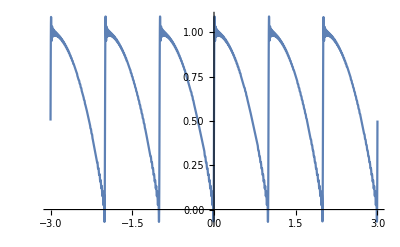

```mathematica
f[t_] := 1 - t^2;
T = 1;
a[0] := 1/T * NIntegrate[f[t], {t, 0 ,T}]
a[i_Integer] := 2/T * NIntegrate[f[t] * Cos[i * (2Pi * t)/T], {t, 0, T}]
b[i_Integer] := 2/T * NIntegrate[f[t] * Sin[i * (2Pi * t)/T], {t, 0, T}]
Vyraz = Sum[a[i]*Cos[i *(2Pi)/T* t] + b[i]*Sin[i *(2Pi)/T * t], {i, 0, 50}];
Plot[f[t], {t, 0, 1}];
Plot[Vyraz, {t, -3, 3}]
```